## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; Q=0.999; r1 = 30; mu = 0.2;
```

```mathematica
winit=(0.25-0.00005*I)
```

0.25-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.262544+4.1269×10^-8 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
qscal = 0.5; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ; wc=qscal*Q/rp
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-I*rp^2*(wres-wc)/(rp-rm);
sigmasol=(qscal*Q*wres+M*mu^2-2*M*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  wres-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

0.478123

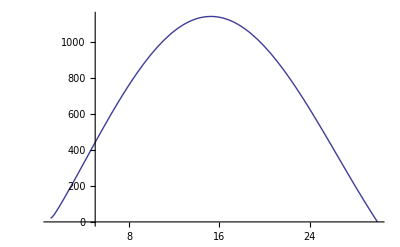

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,rp,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<201,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 +ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);

sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,200}];
t2r=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,200}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.25+0.000001*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
qscal = 0.5 - ie/200; r0=rp+10^(-8); rm=M-Sqrt[M^2-Q^2]; rp=M+Sqrt[M^2-Q^2] ;wc=qscal*Q/rp;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-I*rp^2*(w-wc)/(rp-rm);
sigmasol=(qscal*Q*w+M*mu^2-2*M*w^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[{(1-2*M/r+Q^2/r^2)*D[Rs[r],{r,2}]+(   2/r*( 1-2*M/r+Q^2/r^2) + (  2*M/r^2-2*Q^2/r^3  ) )*D[Rs[r],{r,1}]+(     1/(1-2*M/r+Q^2/r^2)*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2        )*Rs[r]==0,Rs[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(r0-rp)^(rhosol),Rs'[r0]==(rp-rm)^(sigmasol-rhosol-1)*Exp[qsol*r0]*(rhosol)*(r0-rp)^(rhosol-1)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
qscals[ie]=qscal/mu;
winit=wres+0.001;
ie=ie+1

]
t1l=Table[{N[qscals[n],10],Re[witer[n]]},{n,0,100}];
t2l=Table[{N[qscals[n],10],Im[witer[n]]},{n,0,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot :: lstol will be suppressed during this calculation.

{{2.5,4.12687×10^-8},{2.475,3.91054×10^-8},{2.45,3.70165×10^-8},{2.425,3.50008×10^-8},{2.4,3.30632×10^-8},{2.375,3.1185×10^-8},{2.35,2.93825×10^-8},{2.325,2.76479×10^-8},{2.3,2.59823×10^-8},{2.275,2.43822×10^-8},{2.25,2.28468×10^-8},{2.225,2.13756×10^-8},{2.2,1.99675×10^-8},{2.175,1.862×10^-8},{2.15,1.73327×10^-8},{2.125,1.61051×10^-8},{2.1,1.4935×10^-8},{2.075,1.37952×10^-8},{2.05,1.27634×10^-8},{2.025,1.1754×10^-8},{2.,1.08035×10^-8},{1.975,9.90967×10^-9},{1.95,9.06081×10^-9},{1.925,8.26104×10^-9},{1.9,7.50914×10^-9},{1.875,6.80378×10^-9},{1.85,6.14399×10^-9},{1.825,5.52715×10^-9},{1.8,4.95404×10^-9},{1.775,4.42195×10^-9},{1.75,3.92929×10^-9},{1.725,3.47524×10^-9},{1.7,3.05823×10^-9},{1.675,2.67666×10^-9},{1.65,2.32921×10^-9},{1.625,2.01424×10^-9},{1.6,1.73179×10^-9},{1.575,1.47544×10^-9},{1.55,1.24835×10^-9},{1.525,1.04705×10^-9},{1.5,8.69775×10^-10},{1.475,8.03982×10^-10},{1.45,5.789×10^-10},{1.425,4.60205×10^-10},{1.4,3.56285×10^-10},{1.375,2.5627×10^-10},{1.35,1.7843×10^-10},{1.325,9.56437×10^-11},{1.3,1.02023×10^-11},{1.275,-8.92557×10^-11},{1.25,-2.01718×10^-10},{1.225,-3.4356×10^-10},{1.2,-5.28088×10^-10},{1.175,-7.70211×10^-10},{1.15,-1.08737×10^-9},{1.125,-1.50144×10^-9},{1.1,-2.03679×10^-9},{1.075,-2.7224×10^-9},{1.05,-3.59096×10^-9},{1.025,-4.6801×10^-9},{1.,-6.03167×10^-9},{0.975,-7.69268×10^-9},{0.95,-9.71954×10^-9},{0.925,-1.21622×10^-8},{0.9,-1.50908×10^-8},{0.875,-1.85805×10^-8},{0.85,-2.27051×10^-8},{0.825,-2.75532×10^-8},{0.8,-3.322×10^-8},{0.775,-3.98115×10^-8},{0.75,-4.74413×10^-8},{0.725,-5.62338×10^-8},{0.7,-6.63278×10^-8},{0.675,-7.78706×10^-8},{0.65,-9.10241×10^-8},{0.625,-1.05965×10^-7},{0.6,-1.22887×10^-7},{0.575,-1.41998×10^-7},{0.55,-1.6352×10^-7},{0.525,-1.87702×10^-7},{0.5,-2.14804×10^-7},{0.475,-2.45119×10^-7},{0.45,-2.78946×10^-7},{0.425,-3.16624×10^-7},{0.4,-3.58531×10^-7},{0.375,-4.05025×10^-7},{0.35,-4.56549×10^-7},{0.325,-5.13534×10^-7},{0.3,-5.76491×10^-7},{0.275,-6.45925×10^-7},{0.25,-7.22401×10^-7},{0.225,-8.06529×10^-7},{0.2,-8.98948×10^-7},{0.175,-1.00036×10^-6},{0.15,-1.11151×10^-6},{0.125,-1.2332×10^-6},{0.1,-1.3663×10^-6},{0.075,-1.51171×10^-6},{0.05,-1.67042×10^-6},{0.025,-1.84349×10^-6},{0.,-2.03205×10^-6}}

```mathematica
(*The imaginary part vs the radius*)
```

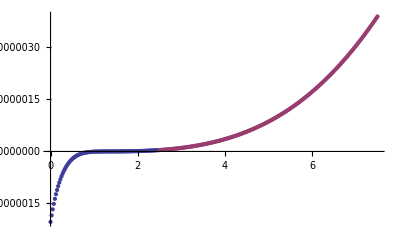

```mathematica
ListPlot[{t2l,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

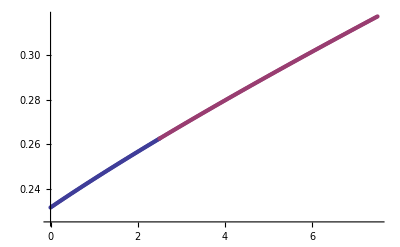

```mathematica
ListPlot[{t1l,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=30/Q=0.999/R.dat",Join[t1l,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=30/Q=0.999/I.dat",Join[t2l,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=30/Q=0.999/R.dat

/home/h/skoli/pt/rnef/mathematica/q/mu0.2/r=30/Q=0.999/I.dat